## Pade Approximant to Delay (Section 3.6.4)

```mathematica
Clear["Global`*"];
```

```mathematica
G1 = PadeApproximant[Exp[-s],{s,0,1}]
```

(1-s/2)/(1+s/2)

```mathematica
G2 = PadeApproximant[Exp[-s],{s,0,2}]
```

(1-s/2+s^2/12)/(1+s/2+s^2/12)

```mathematica
G3 =PadeApproximant[Exp[-s],{s,0,3}]
```

(1-s/2+s^2/10-s^3/120)/(1+s/2+s^2/10+s^3/120)

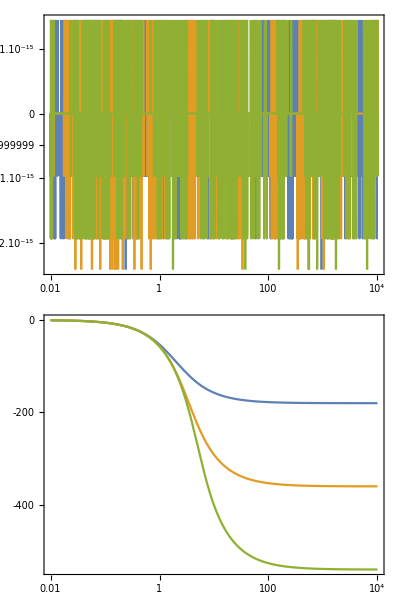

```mathematica
BodePlot[{G1,G2,G3},{0.01,10000}]
```

```mathematica
Solve[1-s/2+s^2/12==0,s]
```

{{s→3-ⅈ √3},{s→3+ⅈ √3}}

```mathematica
Solve[1-s/2+s^2/10-s^3/120==0,s]//N
```

{{s→4.64437},{s→3.67781-3.50876 ⅈ},{s→3.67781+3.50876 ⅈ}}

```mathematica
tmax=3;
G1tf =  TransferFunctionModel[G1,s];
G2tf = TransferFunctionModel[G2,s];
G3tf = TransferFunctionModel[G3,s];
```

```mathematica
y1 = OutputResponse[G1tf,UnitStep[t],t] // Simplify
```

{(1-2 ⅇ^(-2 t)) UnitStep[t]}

```mathematica
y2 = OutputResponse[G2tf,UnitStep[t],t] // Simplify
```

{Piecewise[{{1-4 √3 ⅇ^(-3 t) Sin[√3 t], t≥0}, {0, True}}]}

```mathematica
y3 = OutputResponse[G3tf,UnitStep[t],{t,0,tmax}];
```

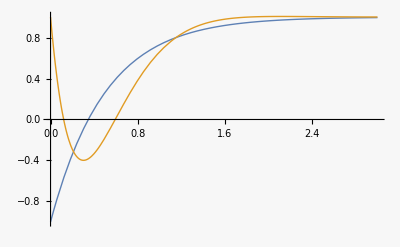

```mathematica
Plot[{y1,y2},{t,0,tmax},PlotRange->Full]
```

```mathematica
Gtest=(ω^2-2ζ ω s+s^2)/(ω^2+2ζ ω s+s^2) /. ζ-> 0.5 /. ω -> 2 Pi
```

(4 π^2-6.28319 s+s^2)/(4 π^2+6.28319 s+s^2)

```mathematica
Gtesttf =  TransferFunctionModel[Gtest,s]
```

(39.4784-6.28319 s+s^2)/(39.4784+6.28319 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1139.4784176043574339.478417604357431FalseFalseFalseAutomaticNoneAutomatic

```mathematica
ytest = OutputResponse[Gtesttf,UnitStep[t],{t,0,5}];
```

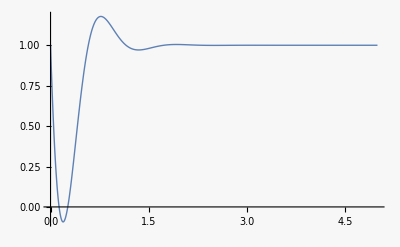

```mathematica
Plot[ytest,{t,0,5},PlotRange->Full]
```

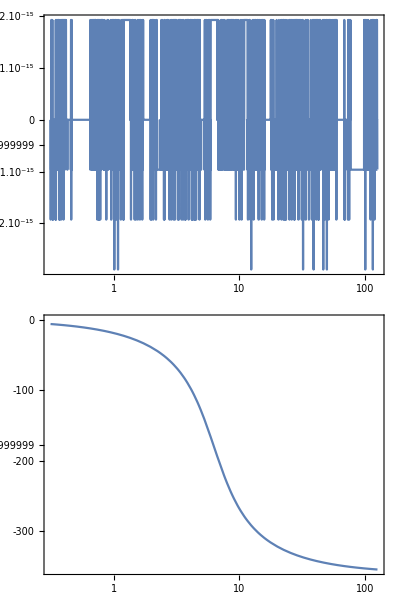

```mathematica
BodePlot[Gtest]
```